```mathematica
SetDirectory[NotebookDirectory[]];
Get["Necessary Functions.m"]
```

{pluck, peak, parametricregion, egsystem, QOtriangleApprox, freqsintens, graphfi, keep, loudfreqs, graphweight, colorfreqs, freqband, freqlines, print3Dborder, print3Dregion, p, vard, disvector,soundanalysispg,comparetheovals}

### Finding multiplicative constant for circles in MMA

```mathematica
bigcircle=DiscretizeRegion[Disk[{0,0},N[385/2]]];
f1bigmeas={104.738,110.25}; (* {min,max} *)f1bigcalc=√NDEigenvalues[{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},u,{x,y}∈bigcircle,1]
```

{0.0125168}

```mathematica
constant=f1bigmeas/f1bigcalc[[1]] (* {min,max} *)
√NDEigenvalues[{-#^2 Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},u,{x,y}∈bigcircle,1]&/@constant
```

{8367.79,8808.15}

{{104.738},{110.25}}

This produces a list depending on the minimum value for the constant and then a list depending on the maximum value for the constant. In other words, bigfreqs[[1,i]] and bigfreqs[[2,i]] are the minimum and maximum of the i’th frequency respectively.

### Big Circle

```mathematica
{bigcsysMin,bigcsysMax}=egsystem[20,#^2][bigcircle]& /@ constant;
```

```mathematica
{graphweight[bigcsysMin[[2]],bigcircle],graphweight[bigcsysMax[[2]],bigcircle]}
```

Threshhold 50 looks like a good option (should be the same for both).

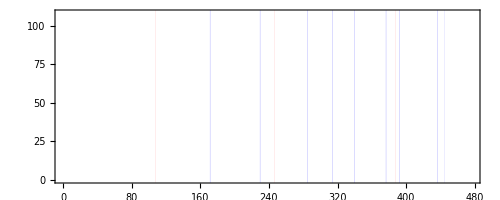

```mathematica
freqlines[bigcsysMin,bigcsysMax,50]
```

```mathematica
bigfreqs=Table[{bigcsysMin[[1,i]],bigcsysMax[[1,i]]},{i,Length[bigcsysMin[[1]]]}]
bigfreqs[[#]]&/@loudfreqs[bigcsysMin[[2]],50]
```

{{104.738,110.25},{166.887,175.67},{166.888,175.67},{223.691,235.463},{223.693,235.466},{240.446,253.1},{277.933,292.559},{277.939,292.566},{305.646,321.731},{305.661,321.747},{330.625,348.025},{330.646,348.047},{366.818,386.122},{366.85,386.156},{377.167,397.016},{382.299,402.418},{382.31,402.43},{425.578,447.975},{425.625,448.024},{433.234,456.034}}

{{104.738,110.25},{240.446,253.1},{377.167,397.016}}

### Medium Circle

```mathematica
medcircle=DiscretizeRegion[Disk[{0,0},N[155/2]]];
{medcsysMin,medcsysMax}=egsystem[20,#^2][medcircle]& /@ constant;
```

```mathematica
{graphweight[medcsysMin[[2]],medcircle],graphweight[medcsysMax[[2]],medcircle]}
```

Threshhold 20 looks good.

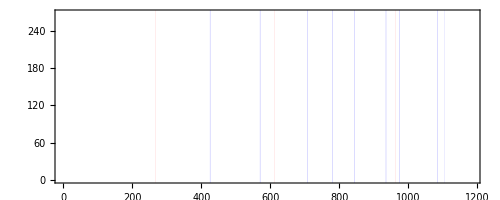

```mathematica
freqlines[medcsysMin,medcsysMax,20]
```

```mathematica
medfreqs=Table[{medcsysMin[[1,i]],medcsysMax[[1,i]]},{i,Length[medcsysMin[[1]]]}]
medfreqs[[#]]&/@loudfreqs[medcsysMin[[2]],20]
```

{{260.156,273.847},{414.526,436.342},{414.528,436.344},{555.619,584.859},{555.625,584.866},{597.234,628.664},{690.344,726.675},{690.353,726.684},{759.161,799.113},{759.181,799.134},{821.233,864.452},{821.238,864.457},{911.076,959.023},{911.146,959.097},{936.783,986.083},{949.52,999.49},{949.606,999.58},{1056.97,1112.6},{1057.06,1112.69},{1076.09,1132.72}}

{{260.156,273.847},{597.234,628.664},{936.783,986.083}}